```mathematica
(* cost of MV sumcheck, relative to the size|H| of the n-dimensional hypercube
*)
ClearAll@sumcheck;
sumcheck[n_,d_,numVars_,{Qm_,Qs_,Qa_}]:=
(1 - 1/2^(n)) * {d*numVars + (d+1) * Qm, (numVars+ d + 1) * Qs, d*numVars + (d+1)*(Qa + 1)}
```

```mathematica
(* From Berstein and Lange, 2007, Analysis of EC single scalar multiplication
*)
costPerScalarBit = 8; (* InvEdwards coordinates *)
costPerScalarMul = 8*255
costPippengerPerScalar = costPerScalarMul/12 (* 1 / log|H|, with |H|=2^12 *)
```

2040

170

```mathematica
maxM = 100;
```

## Based on the logarithmic derivative

### not too large number of columns

```mathematica
arithComp = {4M + 1,1,M+1};
costsumcheck = sumcheck[n, M+3,M+4, arithComp ]/(1 - 1/2^n)//Simplify
cost = costsumcheck+ {7, 1, 2M+1}//Simplify
```

{16+24 M+5 M^2,2 (4+M),20+13 M+2 M^2}

{23+24 M+5 M^2,9+2 M,21+15 M+2 M^2}

### large number of columns

```mathematica
arithComp = {4,1,2};
costsumcheckLargeM = M * sumcheck[n+m, 4, 5, arithComp]/(1 - 1/2^(n+m))//Simplify
costLargeM = costsumcheckLargeM + M * {4, 0, 2}//Simplify
```

{40 M,10 M,35 M}

{44 M,10 M,37 M}

### break even point

{363+24 M+5 M^2,349+2 M,361+15 M+2 M^2}

{44 M+170 (1+M),10 M+170 (1+M),37 M+170 (1+M)}

{{M→1.0445},{M→36.9555}}

36

2.15086

{8}

1.5

{3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

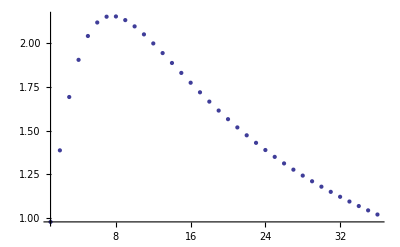

```mathematica
costWithComm = cost + costPippengerPerScalar*2
costWithCommLarge = costLargeM + costPippengerPerScalar*(M+1)

(* break even point with linear strategy *)
sol = NSolve[costWithComm[[1]] == costWithCommLarge[[1]],M]
breakEven = M /. sol // Last//Floor

(* maximum speedup *)
ratio = Table[costWithCommLarge[[1]]/costWithComm[[1]]/.{M->x},
{x,1, breakEven}];
max = Max@ratio;
max//N
Position[ratio,max]//Flatten

(* range for 0.8 of the maximum speedup *)
threshold = 1.5
Position[(#≥threshold)&/@ratio,True]//Flatten

ListPlot[ratio,PlotRange->All]
```

### Best strategy

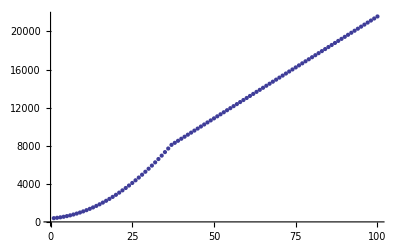

```mathematica
bestCostWithComm = Join[
Table[costWithComm[[1]]/.{M->x},{x,1,breakEven}],
Table[costWithCommLarge[[1]]/.{M->x},{x,breakEven+1,maxM}]
];
ListPlot[bestCostWithComm]
```

## Based on the univariate strategy

### not too large number of columns

```mathematica
arithComp = {2(M+1)+3,2,1};
costsumcheckUV = sumcheck[n, M+3, 2M+6, arithComp]/(1 - 1/2^n)//Simplify
costUV = costsumcheckUV+ {2(M+1), 0, 3M+4}//Simplify
```

{38+25 M+4 M^2,20+6 M,2 (13+7 M+M^2)}

{40+27 M+4 M^2,20+6 M,30+17 M+2 M^2}

### large number of columns

```mathematica
arithComp = {5,2,1};
costsumcheckUVlarge = (M+1) * sumcheck[n+m, 3, 6, arithComp]/(1 - 1/2^(n+m))//Simplify
costUVlarge = costsumcheckUVlarge+ (M+1){7, 0, 4}//Simplify
```

{38 (1+M),20 (1+M),26 (1+M)}

{45 (1+M),20 (1+M),30 (1+M)}

### break even point

{40+27 M+4 M^2+170 (2+M),20+6 M+170 (2+M),30+17 M+2 M^2+170 (2+M)}

{385 (1+M),360 (1+M),370 (1+M)}

{{M→-0.0265807},{M→47.0266}}

47

1.57972

{6}

1.26377

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26}

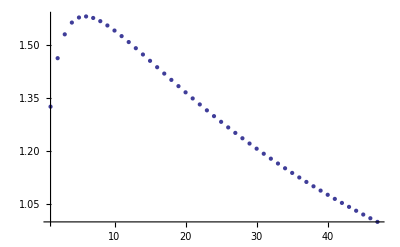

```mathematica
costWithCommUV = costUV + costPippengerPerScalar * (M+2)
costWithCommUVlarge = costUVlarge + costPippengerPerScalar * 2*(M+1)

(* break even point with linear strategy *)
sol = NSolve[costWithCommUV[[1]] == costWithCommUVlarge[[1]],M]
breakEvenUV = M /. sol // Last//Floor

(* maximum speedup *)
ratio = Table[costWithCommUVlarge[[1]]/costWithCommUV[[1]]/.{M->x},
{x,1, breakEvenUV}];
max = Max@ratio;
max//N
Position[ratio,max]//Flatten

(* range for 0.8 of the maximum speedup *)
max * 0.80
Position[(#≥max*0.80)&/@ratio,True]//Flatten

ListPlot[ratio,PlotRange->All]
```

### best strategy

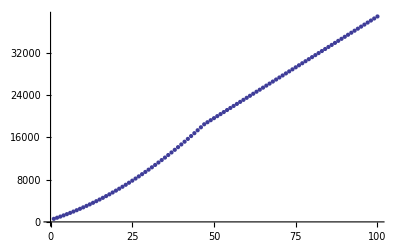

```mathematica
bestCostWithCommUV = Join[
Table[costWithCommUV[[1]]/.{M->x},{x,1,breakEvenUV}],
Table[costWithCommUVlarge[[1]]/.{M->x},{x,breakEvenUV+1,maxM}]
];
ListPlot[bestCostWithCommUV]
```

## Comparison

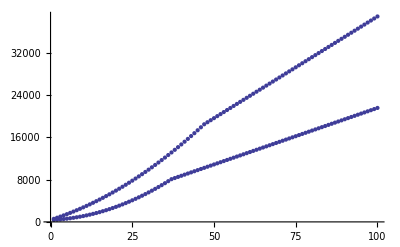

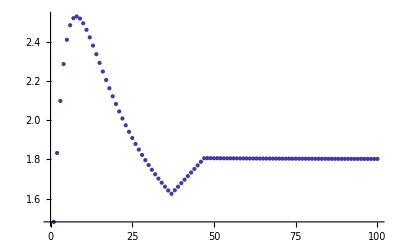

1.48214

2.528

```mathematica
Show[{
ListPlot[bestCostWithCommUV],
ListPlot[bestCostWithComm]
}]
ListPlot[
bestCostWithCommUV/bestCostWithComm
]
bestCostWithCommUV/bestCostWithComm//Min//N
bestCostWithCommUV/bestCostWithComm//Max//N
```